## Section | Dissipative interactions and open quantum systems

The chapter begins by discussing the concept of decoherence and dissipation, emphasizing that while the evolution of isolated quantum systems is unitary and preserves coherence, real-world systems are rarely isolated. We describe the mathematical formalism of open quantum systems, the role of the density matrix in describing mixed states, and the master equation approach to modeling dissipative dynamics. The chapter also explores specific examples, such as the decoherence of superposition states (e.g., Schrödinger cat states) and other phenomena that can be described by master equations.

### Key concepts

Lindblad master equation

Decoherence

Modeling open quantum systems

Workflow for solving master equations

### 8.1 Quantum jump approach and decoherence

Quantum theory was initially developed as a theory based on ensembles because it was thought that manipulating single quantum systems (like one electron or one atom) was impossible. In 1975 Dehmelt proposed in the context of fluorescence spectroscopy some schemes for measuring transition frequencies that required single quantum system observations, that were later implemented using single ion traps. Predictions were confirmed by experiments that impulsed the development of the quantum jump approach

#### Algorithm description

The quantum jump algorithm is similar to Monte Carlo methods, we assume a cavity field at T = 0 K,  and photon emission is represented by the annihilation operator â. We can describe the algorithm with the following steps

Calculate the current probability ΔP of emission of a photon in a time interval δt according to Δ P=γ ⟨ψ|(â)^†â|ψ⟩ δ t where |ψ⟩ is one member of the ensemble

Obtain a random number 0 ≤ r < 1, compare with ΔP to decide emission

Emit if r < ΔP (field loses one photon), the system jumps to renormalized form |ψ⟩→|ψ_emit⟩=(â|ψ⟩)/(⟨ψ|(â)^†â|ψ⟩^(1/2))

No emission r > ΔP, the system evolves according to
|ψ⟩→|ψ_(no emit)⟩=(e^(-ⅈ δ t H_eff)|ψ⟩)/([⟨ψ|e^(ⅈ δ t H_eff^†) e^(-ⅈ δ t H_eff)|ψ⟩]^(1/2))=(e^(-ⅈ δ t H_eff)|ψ⟩)/([⟨ψ|e^(-γ δ t (â)^†â)|ψ⟩]^(1/2))
≈([1-(ⅈ/ℏ)Ĥ δ t-(γ/2)δ t (â)^†â]|ψ⟩)/(1-Δ P)^(1/2)
where (Ĥ)_eff=Ĥ-ⅈ ℏ (γ/2)(â)^†â is the effective non Hermitian Hamiltonian describing non unitary evolution, where the second term represents decay of the cavity field.

Iterate the process to record a trajectory of conditional evolution of one member of the ensemble with jump events  t_(1,)t_2...

Average observables over a big number of trajectories to get average behavior of the whole ensemble

#### Quantum jumps on familiar states

Let’s assume Ĥ = 0 so only the dissipation acts. If we have an initial cavity field in a coherent state |α⟩ the jump evolution leaves the field unchanged because a coherent state is an eigenstate of the annihilation operator, and the no jump-evolution results:

(e^(-(γ/2)δ t a^†a)|α⟩)/(√⟨α|e^(-γ δ t a^†a)|α⟩)=|α e^(-γ δ t/2)⟩

The coherent state remains a coherent state after the evolution, however, the amplitude of the state has an exponential decay due to the non unitary Hamiltonian

Set truncation size:

```mathematica
SetFockSpaceSize[20];
```

Term describing non unitary evolution:

```mathematica
Hdisp=1/2 (-ⅈ) h γ SuperDagger[a]@a;
```

Let’s verify the equation symbolically:

```mathematica
(ⅇ^(-(ⅈ Hdisp δt)/h))[CoherentState[][α]]==CoherentState[][α ⅇ^(1/2 (-γ) δt)]
```

True

We get a valid result because the square root in the denominator is just a normalization factor. QuantumState  equality (==) in Wolfram QuantumFramework works up to global phases and multiplicative factors

Check the dissipative Hamiltonian is not unitary:

```mathematica
Hdisp["UnitaryQ"]
```

False

If we now consider a cavity field prepared in a even cat state  (|ψ⟩)_e=𝒩_e(|α⟩+|-α⟩) where 𝒩_e   is  a normalization constant , the annihilation operator converts an even cat state to odd cat state

Photon distribution corresponds to odd cat state after jump:

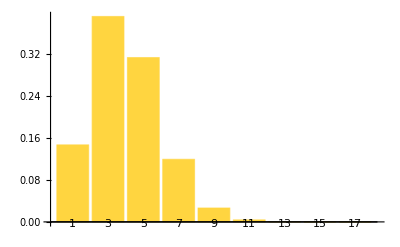

```mathematica
(a @ CatState[][2.,0])["ProbabilityPlot"]
```

For a no jump transition the field state decays as

exp(-γ δ t (â)^†â/2)(|α⟩±|-α⟩)=(|α e^(-γ δ t/2)⟩±|-α e^(-γ δ t/2)⟩)

We will also verify this symbolically without normalizing, that is why we will not use CatState (which comes normalized). Instead, we define a superposition of not-normalized coherent states

Coherent state superposition:

```mathematica
evenCat=QuantumState[Total[(CoherentState["Normalized"->False][#1]&)/@{α,-α}],"Parameters"->α];
```

“No-jump” evolution:

```mathematica
(ⅇ^(- ⅈ Hdisp /h δt)) @ evenCat  == evenCat[α ⅇ^(-γ δt /2)]
```

True

The cat state “reduces”  during the no-jump evolution (the amplitude decays)

### Decoherence

It can be defined as the transformation over time of a quantum mechanical superposition into a classical statistical mixture, as a result of interaction with an environment. As an example, consider  an initial even cat state , the cavity-environment state is

|ψ(0)⟩∝(|α⟩+|-α⟩)|ϵ⟩

where |ϵ ⟩ is the quantum state of the environment. The environment can be described  with an arbitrary number of systems and states which are not relevant for the analysis. At a later time the system will evolve to

|ψ(t)⟩∝(|β⟩|ϵ_1⟩+|-β⟩|ϵ_2⟩)

such that β=α e^(-γ t/2)   from the previous section, so that the field becomes entangled with the environment. If we compute the density operator and trace over a complete set of states of the environment ⟨ϵ_i|ϵ_j⟩=δ_ij, we get a reduced field density operator

ρ_F(t)=Tr_Env ρ(t)=∑_i ⟨ϵ_i|ρ|ϵ_i⟩=|β(t)⟩⟨β(t)|+|-β(t)⟩⟨-β(t)|

is a statistical mixture of two coherent states

#### Quantum jump implementation

Let’s implement the quantum jump algorithm of the previous section, the quantum jump algorithm is also known in literature as the Monte Carlo wave function (MCWF) method. This will also give more intuition about why that exponential decay factor appears in the equations

Setup simulation parameters:

```mathematica
dim=8;
γ=0.5;
δt=0.01;
steps=600;
```

Annihilation and number operators:

```mathematica
aOp=AnnihilationOperator[dim]["Matrix"];
nOp=ConjugateTranspose[aOp]. aOp ;
```

Define the non-Hermitian Hamiltonian, we assume pure dissipation so the coherent Hamiltonian is zero:

```mathematica
Heff=-ⅈ (γ/2) nOp;
U0=MatrixExp[-ⅈ Heff δt];
```

Consider as an initial state |4⟩:

```mathematica
ψInitial=FockState[4,dim]["StateVector"];
```

Implement the jump function, based on the algorithm that was described before:

```mathematica
takeStep[ψ_]:=Module[{ΔP,ψNew},
ΔP=γ δt Re[Conjugate[ψ].nOp.ψ];
If[RandomReal[]<ΔP,
(*JUMP*)
ψNew=aOp.ψ,
(*NO JUMP*)
ψNew=U0.ψ];
ψNew/Norm[ψNew]]
```

Run the quantum jump algorithm for 1000 trajectories, and track the mean photon number for each trajectory and calculate the average of all trajectories:

```mathematica
SeedRandom[42];
numTrajectories=1000;
Print["Simulating ",numTrajectories," trajectories..."];
allTrajectories=Table[NestList[takeStep,ψInitial,steps],{numTrajectories}];
Print["Simulation completed. "]
allPhotonNumbers=Map[Function[traj,Map[Re[Conjugate[#].nOp.#]&,traj]],allTrajectories];
averagePhotonNumbers=Mean[allPhotonNumbers];
```

Simulating 1000 trajectories...

Simulation completed.

Plot the results of every trajectory:

```mathematica
Show[ListLinePlot[allPhotonNumbers,],ListLinePlot[averagePhotonNumbers,],]
```

-Graphics-

Observing a single quantum trajectory reveals a sequence of discrete, random downward steps, directly mirroring the isolated ‘clicks’ of a photon detector. However, when we average these individual trajectories over a large ensemble, the discrete jumps wash out, giving rise to smooth, continuous evolution. This emergent average behavior perfectly recovers the expected exponential decay, ⟨(n⟩)_(t=0)ⅇ^(-γ t). It is precisely this ensemble-averaged dynamic that is captured by a master equation, which we will formalize next

### Master equation for density operators

The history of a particular trajectory splits into two alternatives in a time Δt to allow at most one jump, either it jumps or it does not

|ψ⟩→Piecewise[{{(|ψ⟩)_emit, with probability   Δ P}, {(|ψ⟩)_(no emit), with probability   1-Δ P}}]

Assuming a simple case of a pure state the density operator is|ψ⟩⟨ψ|, so the evolution can be described as a sum of two outcomes:

|ψ⟩⟨ψ|→Δ P |ψ_emit⟩⟨ψ_emit|+(1-Δ P)|ψ_(no emit)⟩⟨ψ_(no emit)|

=γ δ t â|ψ⟩⟨ψ|(â)^†+[1-ⅈ/ℏ Ĥ δ t-γ/2 δ t (â)^†â]|ψ⟩⟨ψ|[1+ⅈ/ℏ Ĥ δ t-γ/2 δ t (â)^†â]

≈|ψ⟩⟨ψ| -ⅈ/ℏδ t [Ĥ,|ψ⟩⟨ψ|]
+γ/2δ t (2 â|ψ⟩⟨ψ|(â)^†-(â)^†â|ψ⟩⟨ψ|-|ψ⟩⟨ψ|(â)^†â)

The analysis can be extended to more general density operators

Averaging  over all the members of the ensemble:

ρ̂(t+δ t)=ρ̂(t)-ⅈ/ℏδ t [Ĥ,ρ̂]+γ/2 δ t (2 â ρ̂(â)^†-(â)^†â ρ̂-ρ̂(â)^†â)

Taking the limit as δt → 0 we get a differential equation

(d ρ̂)/dt=-ⅈ/ℏ[Ĥ,ρ̂]+γ/2(2 â ρ̂(â)^†-(â)^†â ρ̂-ρ̂(â)^†â)

Referred as the master equation which can also be obtained from more complicated methods for the T=0K damping problem

This is a particular case of a more general equation called the Lindblad equation

ρ̇=-ⅈ [H,ρ]+ ∑_n γ_n(L_n ρ L_n^†-1/2{L_n^†L_n,ρ})

where L_n are called jump operators representing the effects of the environment, and those operators have associated γ_n rates

Considering just  n=1 with the jump operator â (related to photon loss) with rate γ we get the previous equation:

```mathematica
-ⅈ/h HoldForm[Commutator[H,ρ]]+Simplify[γ(a**ρ**SuperDagger[a]-1/2 Anticommutator[SuperDagger[a]**a,ρ])]
```

1/2 γ (2 a**ρ**a^†-ρ**a^†**a-a^†**a**ρ)-(ⅈ Hρ)/h

The whole equation can be cast in super-operator form, such that the right hand side is the Lindblad super-operator ℒ applied to some density operator ρ

ρ̇=ℒ[ρ]

The Lindblad master equation is a matrix differential equation. Most standard numerical ODE solvers (like Runge-Kutta) are designed to solve systems of vector differential equations. Therefore, we need a mathematical trick to reshape our N × N  density matrix ρ into an N^2×  1 column vector denoted as |ρ⟩⟩. Consequently, the operators acting on ρ from the left and right must be upgraded into an N^2× N^2 super-operator matrix.

One convention is to use row-stacking (stack rows of a matrix into a vector)

ρ=(ρ_11 | ρ_12
ρ_21 | ρ_22)   →^vec_R    |ρ⟩⟩=(ρ_11
ρ_12
ρ_21
ρ_22)

Using row-stacking vectorization we can express the terms of the Lindblad equation that will act on the vectorized density operator as

-ⅈ[H,ρ]->-ⅈ(H⊗𝕀-𝕀⊗H^T)
𝒟_vec[L_μ]=L_μ⊗L_μ^*-1/2(L_μ^†L_μ⊗𝕀+𝕀⊗(L_μ^†L_μ)^T)

Dissipator contribution, represent each of the terms in the sum of Lindblad equation, this definition includes the case L_i≠ L_j (non-diagonal form of Lindblad equation) but we will stick to the case 𝒟(L_i)

```mathematica
ClearAll[𝒟]
𝒟[Lj_,Lk_]:=KroneckerProduct[Lj,Conjugate[Lk]]-1/2(KroneckerProduct[ConjugateTranspose[Lk].Lj,IdentityMatrix[Length[Lk]]]+KroneckerProduct[IdentityMatrix[Length[Lk]],Transpose[ConjugateTranspose[Lk].Lj]])
𝒟[Lj_]:=𝒟[Lj,Lj]
```

Lindbladian builder:

```mathematica
Lindbladian[h_,lk_,γk_?VectorQ]:=-ⅈ(KroneckerProduct[h,IdentityMatrix[Length@h]]-KroneckerProduct[IdentityMatrix[Length@h],Transpose@h])+γk.Map[𝒟,lk]
```

We can use “Liouvillian” in QuantumOperator to get those super-operators, for example consider a two level system with H=σ_z , L_1=σ_x with rate γ:

```mathematica
Clear[γ];
ℒ =QuantumOperator["Liouvillian"[QuantumOperator["Z"],{QuantumOperator["X"]},{γ}]]
```

-γ0000+(-2 ⅈ-γ)0011+γ0101+γ0110+γ1001+γ1010+(2 ⅈ-γ)1100-γ1111

ℒ is a super-operator:

```mathematica
ℒ["Type"]
```

Superoperator

Check the dimensions of the super-operator matrix:

```mathematica
ℒ["Matrix"]//Dimensions
```

{4,4}

Get the matrix of the Lindbladian using the manual builder:

```mathematica
Lindbladian[PauliMatrix[3],{PauliMatrix[1]},{γ}]//MatrixForm
```

(-γ | 0 | 0 | γ
0 | -γ-2 ⅈ | γ | 0
0 | γ | -γ+2 ⅈ | 0
γ | 0 | 0 | -γ)

Verify we get the same result compared to the matrix of the super-operator object:

```mathematica
ℒ["Matrix"]-Lindbladian[PauliMatrix[3],{PauliMatrix[1]},{γ}]
```

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

### 8.2 Dissipative interactions from master equations

We will see examples of time evolution under dissipative interactions using the functionalities of Wolfram Quantum Framework. We saw how to obtain the Lindbladian, after defining it we can pass to QuantumEvolve to compute the time evolved state

#### Dissipation of a coherent state

Let’s start exploring the dissipation of a coherent state |α⟩ subjected to photon loss

Set the cutoff size:

```mathematica
SetFockSpaceSize[15];
```

Define initial parameters for a coherent state |α⟩ with |α| equal to 2:

```mathematica
αcoh=2 Exp[ⅈ RandomReal[{0,2 π}]];
ρ0=CoherentState[][αcoh];
```

Establishing a damping parameter:

```mathematica
γ = RandomReal[{1,2}];
```

Setting up the Liouvillian master equation with Ĥ= (â)^†â and L_1=â (photon loss):

```mathematica
ℒ= QuantumOperator["Liouvillian"[SuperDagger[a]@a,{a},{γ}]];
```

Computing the evolution numerically (ⅈ included for super-operators):

```mathematica
ρt=QuantumEvolve[ⅈ ℒ,ρ0,{t,0,1}];
```

Helper variables for computing the evolution statistics:

```mathematica
time=Range[0,1,0.01];
fock=Range[$FockSize]-1;
```

Computing mean number of photons and the fidelity with respect to an analytical solution (that remains a coherent state):

```mathematica
qs=QuantumSimilarity[CoherentState[][αcoh ⅇ^(-ⅈ #) ⅇ^(-1/2 # γ)],ρt[#]]&/@time;
meanN=Chop[fock.Diagonal[ρt[#]["DensityMatrix"]]]&/@time;
```

Plotting the statistics, the evolved state behaves like the analytical solution with an exponential decay in the mean number of photons:

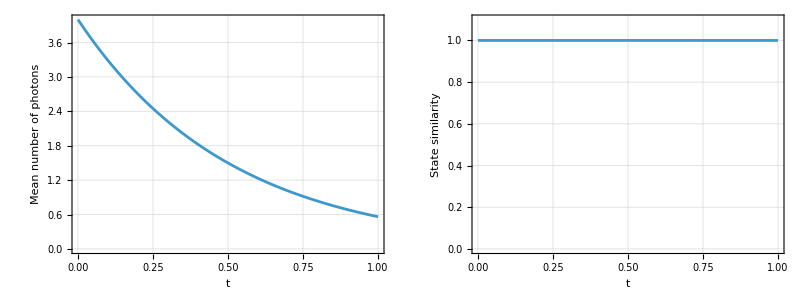
-Graphics-Evolution statistics of a coherent state

```mathematica
Labeled[Grid[{{ListLinePlot[Thread[{time,meanN}],],ListLinePlot[Thread[{time,qs}],]}}],]
```

|α|^2 ⅇ^(-γ t) is the functional form of the mean photon number curve. Then the decay time of the field energy is T_decay=1/γ

Do an exponential decaying fit:

```mathematica
nlm =NonlinearModelFit[Thread[{time,meanN}],k Exp[-g t],{k,g},{t}];
```

Fitted equation:

```mathematica
nlm["Function"][t]
```

3.99977 ⅇ^(-1.96321 t)

Compare the parameters:

```mathematica
(g /. nlm["BestFitParameters"]) - γ
```

4.06697×10^-8

Spiral motion of the center of the Wigner representation of the coherent state, the Hamiltonian with unit frequency makes the coherent state rotate, and the dissipation makes it go towards the origin:

-Graphics-

#### Decoherence of an even cat state : becoming statistical mixture

Set up the cutoff:

```mathematica
SetFockSpaceSize[15];
```

Now we analyze the evolution of  a cavity prepared initially with an even cat state |α|=2 :

```mathematica
αcoh=2 Exp[ⅈ RandomReal[{0,2 π}]];
ρ0=CatState[][αcoh,0];
```

Setting a pure decoherence master equation with photon loss (H = 0):

```mathematica
γ = 0.9;
ℒ= QuantumOperator["Liouvillian"[None,{a},{γ}]];
```

Evolving the state:

```mathematica
ρt = QuantumEvolve[ⅈ ℒ, ρ0, {t,0,10}];
```

Monitoring how the traces change. Tr[(ρ̂)^2]is related to the purity and also a measure of decoherence. But there will be a turning point that purity starts to increase after decreasing, because the decay in energy makes state converge towards the vacuum (pure state) :

Sampling time:

```mathematica
time=Range[0,10,0.01];
```

Compute trace and purity:

```mathematica
traces = Table[{Tr[ρt[t]],ρt[t]["Purity"]},{t,time}];
```

Plot result:

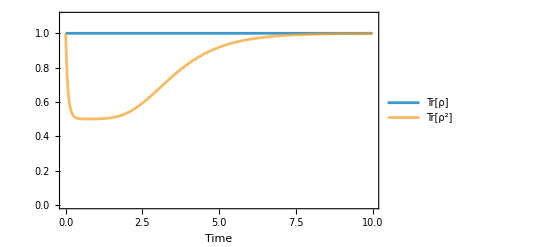

```mathematica
ListLinePlot[Thread[{time,#}]&/@Transpose[traces]
,]
```

The energy decay (mean photon number) still decays exponentially as expected :

```mathematica
meanPhotons = Table[{t,Dot[fock,Diagonal[ρt[t]["DensityMatrix"]]]},{t,time}] ;
```

Plot the curve:

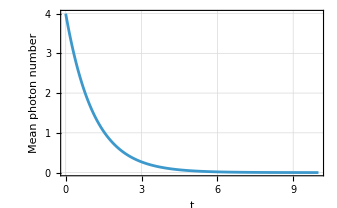

```mathematica
ListLinePlot[meanPhotons,]
```

The theoretical solution of the master equation  is:

ρ_F(t)=𝒩_e^2 [|α e^(-γ t/2)⟩⟨α e^(-γ t/2)|+|-α e^(-γ t/2)⟩⟨-α e^(-γ t/2)|
+e^(-2(|α|)^2(1-e^(-γ t)))(|α e^(-γ t/2)⟩⟨-α e^(-γ t/2)|+|-α e^(-γ t/2)⟩⟨α e^(-γ t/2)|)]

Implement analytical solution:

```mathematica
sol =With[{α=αcoh ⅇ^(1/2 (-γ) t),decay=ⅇ^(-2 Abs[αcoh]^2 (1-ⅇ^(-γ t)))},With[{cPlus=CoherentState[][α],cMinus=CoherentState[][-α]},QuantumState[(cPlus["MatrixState"]+cMinus["MatrixState"]+QuantumOperator[(decay (cPlus@SuperDagger[cMinus]+cMinus@SuperDagger[cPlus]))]["MatrixQuantumState"]),"Parameters"->t]["Normalize"]]];
```

Compute fidelity as function of time:

```mathematica
similarities = Table[QuantumSimilarity[ρt[t],sol[t]],{t,0,10,0.05}];//EchoTiming
```

25.154

Verifying are the same(basically 1 with  numerical error):

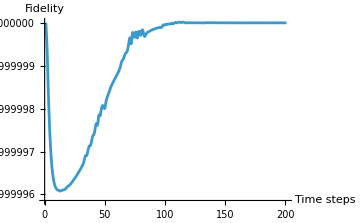

```mathematica
ListLinePlot[similarities,]
```

Apart  from the energy decay we can see there is another quantity that decays,  the the value of e^(-2(|α|)^2(1-e^(-γ t))) multiply the “coherences”(off diagonal elements). For short times a decoherence time is obtained from an expansion T_decoh=1/(2 γ (|α|)^2)=T_decay/(2(|α|)^2). Such that T_decoh<T_decay as long as |α|^2>0.

This can be visualized with the Wigner representation, using some time in between T_decay and T_decoh:

```mathematica
Tevol = 1/(2γ);
```

Statistical mixture of coherent states:

```mathematica
ρmix = Mean[CoherentState[][#]["MatrixState"]&/@{αcoh,-αcoh}];
```

Plot the Wigner function of the states:

```mathematica
GraphicsRow[Table[wig = WignerRepresentation[s[[1]],{-5,5},{-5,5}];DensityPlot[wig[x,p],{x,-5,5},{p,-5,5},],{s,{{ρt[Tevol],"Evolution at t = 1/2γ"},{ρmix,"Statistical Mixture"}}}],]
```

-Graphics-

This verifies that the “coherences” decay faster than the energy and the evolved state becomes a statistical mixture, of course the amplitude is not the same because during the evolution  photon loss has acted

But after a sufficient time the photon loss transforms the state into the vacuum:

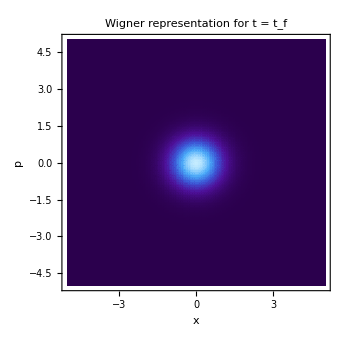

```mathematica
wig = WignerRepresentation[ρt[10],{-5,5},{-5,5}]; DensityPlot[Chop@wig[x,p],{x,-5,5},{p,-5,5},]
```

```mathematica
QuantumSimilarity[ρt[10],FockState[0]]
```

0.999753

### 8.3 Generation of coherent states from decoherence: optical balance

Dissipation destroys coherence in quantum superposition effects. However, even if it does not sound intuitive, it is also possible to create “coherence” from dissipative effects. The master equation has unitary(the commutator term)and non-unitary terms(dissipation) with nonlinear behavior in the creation and annihilation operators. It possible that the interactions can “balance each other” such that the evolution at t → ∞  converges to a different state than the vacuum.

Considering an interaction Hamiltonian OverHat[H_I] = h G(â+(â)^†)  where G is the strength of a pump field that propagates in a photon absorbing medium (dissipation). The master equation then can be described as:

(d ρ̂)/dt=-ⅈG[â+(â)^†,ρ̂]+γ/2(2 â ρ̂(â)^†-(â)^†â ρ̂-ρ̂(â)^†â)

```mathematica
SeedRandom["Lindblad"];
```

We start with a random cavity field:

```mathematica
ρ0 = QuantumState["RandomPure",$FockSize];
```

Establishing simulation parameters, driving strength and photon loss rate:

```mathematica
G = RandomReal[{1,2}];
γ  = RandomReal[{1.5,2}];
```

For the Lindbladian of the master equation we now consider a driving interaction term so Ĥ≠ 0:

```mathematica
ℒ= QuantumOperator["Liouvillian"[G(a+SuperDagger[a]),{a},{γ}]];
```

Solving the master equation numerically:

```mathematica
ρt =QuantumEvolve[ ⅈ ℒ,ρ0,{t,0,3}];
```

The steady-state solution of the equation can be shown to converge to ρ = | β ⟩ ⟨β | where β = - 2 ⅈ G/γ

Compute the fidelity between the evolved state and the proposed solution:

```mathematica
similarities= Table[{t,QuantumSimilarity[ρt[t],CoherentState[][-I 2G/γ]]},{t,0,3,0.1}];
```

Plot state-fidelity, we see it approaches 1 as time evolves:

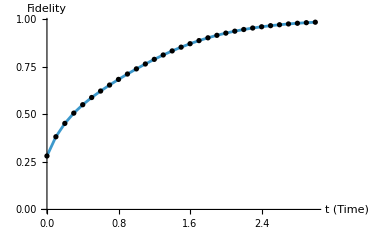

```mathematica
ListLinePlot[similarities,]
```

We can find the steady state of the evolution when ρ̇=0, which amounts to finding the null space of ℒ or solving ℒ(ρ)=0:

```mathematica
ρsteady = Partition[NullSpace[ℒ["Matrix"]][[1]],$FockSize];
```

Fidelity distance between the steady state and |-2ⅈ G/γ⟩, a distance returns how far are the states apart:

```mathematica
QuantumDistance[QuantumState[ ρsteady,$FockSize]["Normalize"],CoherentState[][-I 2G/γ]]
```

6.2135×10^-10

If we have an initial vacuum state  ρ̂(0) = |0⟩ ⟨0| at short enough times we ignore dissipation. The evolution will be unitary and we will get a coherent state  of the form | -ⅈ G t ⟩⟨- ⅈ G t | independent of γ . Fidelity remains around 1 for small times until the approximation is no longer valid

Evolving the ground state:

```mathematica
ρt =QuantumEvolve[ ⅈ ℒ,FockState[0],{t,0,3}];
```

Auxiliary variables for time steps and Fock numbers:

```mathematica
time = Range[0,1.,0.02];
fock =Range[$FockSize]-1;
```

Computing fidelity and mean photon number:

```mathematica
qs = QuantumSimilarity[CoherentState[][-I G #],ρt[#]]& /@ time;
meanN = Chop[fock.Diagonal[ρt[#]["DensityMatrix"]]]& /@ time ;
```

Plot the statistics:

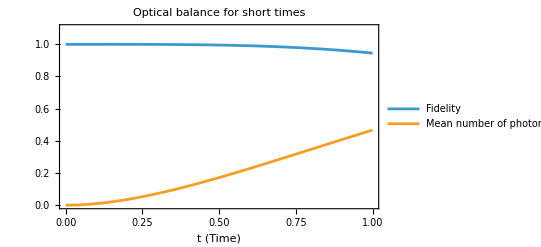

```mathematica
ListLinePlot[Thread[{time,#}]&/@{qs,meanN},]
```

We see there is  point where the fidelity starts to decrease signaling the approximation starts to differ with the exact result

Compute the time where the fidelity goes below 0.99:

```mathematica
tOnset = Extract[time,FirstPosition[qs,x_/;x<0.99]]
```

0.62

At the calculated time we can propose it is a numerical estimator to indicate when the approximation is starting to difer

### 8.4 Thermalization master equation

A thermalization master equation in quantum optics describes how a system (e.g., a qubit or harmonic oscillator) drives towards a thermal Gibbs state ρ_th=ⅇ^(-β H)/Z via interaction with a reservoir. Under Born-Markov and rotating-wave approximations, this typically yields a Lindblad master equation with damping and excitation rates satisfying local detailed balance

Master equation:

dρ/dt=-ⅈ[H,ρ]+κ(n_th+1)𝒟[â]ρ+κ n_th 𝒟[(â)^†]ρ

where n_th is the thermal photon number that is dependent on temperature and frequency of the cavity, and κ is the decay photon rate. We now include both a and a^† as Lindblad jump operators(photon loss and photon injection channels)

Set up truncation size:

```mathematica
SetFockSpaceSize[25];
```

Final evolution time:

```mathematica
tf = 10.;
```

Setting the master equation (Ĥ=ℏ ω a^†a) with the relevant jump operators:

```mathematica
ℒ = QuantumOperator["Liouvillian"[ ω SuperDagger[a]@a,{a,SuperDagger[a]},{κ(nth+1),κ nth}],"Parameters"->{ω,κ,nth}];
```

Pick some parameters, for example n_th = 3, ω = 1, κ = 0.6 :

```mathematica
lindbladian=ℒ[1,0.6,3];
```

Calculating mean number of photons for different initial Fock states:

```mathematica
meanPhotons =
Table[ρt = QuantumEvolve[ⅈ lindbladian ,FockState[i],{t,0,tf}];Table[{t,Dot[Range[0,$FockSize-1],Diagonal[ρt[t]["DensityMatrix"]]]},{t,0,tf,0.01}],{i,{0,1,4}}];
```

Plot mean number of photons curves for the Fock states, see the convergence towards n_th:

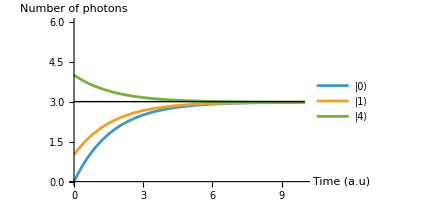

```mathematica
ListLinePlot[meanPhotons,]
```

It indeed converges to a thermal state with n_th mean number of photons:

```mathematica
QuantumSimilarity[ρt[tf],ThermalState[3.]]
```

1.

Find the steady state of the Lindbladian:

```mathematica
ρsteady =Chop[Partition[NullSpace[lindbladian["Matrix"]][[1]],$FockSize]];
```

Verify it is the thermal state with n_th=3:

```mathematica
Chop[QuantumState[ρsteady,$FockSize]["Normalize"]-ThermalState[3.]]
```

0

We can also simulate the evolution for different values of κ to see how it affects the convergence of the state

Compute evolved states varying κ:

```mathematica
evolved =Table[QuantumEvolve[ⅈ ℒ[1,k,3],FockState[0],{t,0,tf}],{k,{0.5,1.,1.5}}];
```

Calculate again the mean number of photons:

```mathematica
meanPhotons =Table[{t,Dot[Range[0,$FockSize-1],Diagonal[#[t]["DensityMatrix"]]]},{t,0,tf,0.01}]&/@evolved;
```

Plot the curves, we see change in the rate of convergence such that higher κ converges faster:

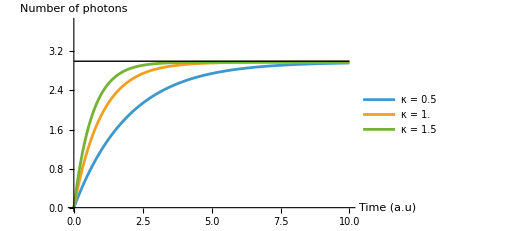

```mathematica
ListLinePlot[meanPhotons,]
```

### 8.5 Jaynes-Cummings with dissipation

We revisit the Jaynes-Cummings model but now including jump operators related to energy dissipation. The proposed master equation is :

Ĥ=ℏ ν (â)^†â+1/2 ℏ ω σ_z+ℏ g (σ_- (â)^†+σ_+ â)

(d ρ)/(d t)=-ⅈ/ℏ[Ĥ,ρ]+𝒟[σ_-]ρ+𝒟[â]ρ

The jump operators are  L_decay=√γ_1(σ_- ⊗ ℐ) and L_loss = √γ_2(ℐ ⊗ a) associated to dissipation rates γ_1 and γ_2 , the atom decaying or the field losing photons

Annihilation operator in the second qudit:

```mathematica
a:= AnnihilationOperator[{2}];
```

Atomic operators:

```mathematica
atomBasis = QuantumBasis[{"e","g"}];
σplus = QuantumOperator["+",atomBasis];
σminus = QuantumOperator["-",atomBasis];
```

Setting up parameters for field frequency, atomic frequency and interaction coupling, we consider a resonant case (ν = ω)

```mathematica
SetFockSpaceSize[12];
ν = 10.;   (* field frequency *)
ω = 10.;   (* atomic frequency *)
gc = 15.; (* interaction coupling strength *)
```

Let’s consider an initial state |e⟩ |n⟩ with n = 2:

```mathematica
ψ0 = QuantumTensorProduct[QuantumState["0",atomBasis],FockState[2]]
```

e2

Jaynes-Cummings Hamiltonian:

```mathematica
H =  ν SuperDagger[a]@a+ 1/2 ω QuantumOperator["Z",atomBasis]+gc (σplus@a+σminus@SuperDagger[a]);
```

Get the probability of finding the atom in the excited state:

```mathematica
atomProb[evolved_,tspecs_]:=With[{pe=Re@QuantumPartialTrace[evolved,{2}]["DensityMatrix"][[1,1]]},Table[{t,pe},Evaluate[{t,Sequence@@tspecs}]]]
```

Let’s calculate the evolution for different damping parameters such that γ_1=γ_2, saving the probability of finding the atom in the excited state. QuantumOperator  also admits the “Hamiltonian” syntax to include jump operators, ⅈ is not needed when using QuantumEvolve in this case.  And the jump operators can be specified in their respective subspace because it works with automatic identity padding (σ^- and a)

```mathematica
probsE = Table[ℋ = QuantumOperator["Hamiltonian"[H, {σminus, a}, {x, x}]];
   atomProb[QuantumEvolve[ ℋ, ψ0, {t, 0, 2}],{0,2,0.01}],
   {x, {0.8, 0.4, 0.2}}];
```

Visualize damped Rabi oscillations:

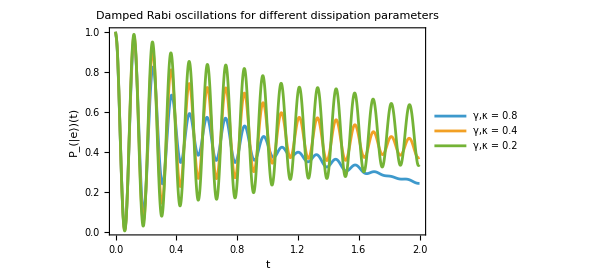

```mathematica
ListLinePlot[probsE,]
```

#### Strong coupling, the crossover and the Purcell regime

Consider the state with one quantum of energy:

```mathematica
ψe0=QuantumTensorProduct[QuantumState["0",atomBasis],FockState[0]]
```

e0

With one excitation the problem can be solved exactly. Only |e,0⟩ and |g,1⟩ take part in the coherent exchange, and either loss sends the system to |g,0⟩ which never comes back. So P_e=|c_e|^2 where the amplitudes obey the “no-jump” equations:

(ⅆ c_e)/ⅆt=-γ/2 c_e-ⅈ g c_1  ,   (ⅆ c_1)/ⅆt=-κ/2 c_1-ⅈ g c_e

Define the 2×2 matrix and calculate the eigenvalues:

```mathematica
noJump={{-γ/2,-ⅈ g},{-ⅈ g,-κ/2}};
Simplify[Eigenvalues[noJump]]
```

{1/4 (-γ-√((γ-κ)^2-16 g^2)-κ),1/4 (-γ+√((γ-κ)^2-16 g^2)-κ)}

We can identify three regimes based on the eigenvalues

Strong coupling  g>(|κ-γ|)/4 the square root is imaginary the excitation oscillates between atom and cavity the vacuum Rabi oscillation under a decaying envelope

The crossover  g=(|κ-γ|)/4  the two eigenvalues merge and the oscillation stops

Purcell regime   κ >> g  a photon leaves the cavity before it can be reabsorbed, so the atom simply decays  but in a faster manner the rate 4 g^2/κ is the Purcell enhancement

The solution is the matrix exponential of Mt applied to (1,0), the excited atom:

```mathematica
peExact[κv_,γv_][τ_]:=Abs[First[MatrixExp[(noJump/.{g->gc,κ->κv,γ->γv}) τ].{1,0}]]^2;
```

Change to g=1:

```mathematica
gc=1.;
H =  ν SuperDagger[a]@a+ 1/2 ω QuantumOperator["Z",atomBasis]+gc (σplus@a+σminus@SuperDagger[a]);
```

Set up value of rates per regime:

```mathematica
regimes={{0.4,0.1},{4.1,0.1},{20.,0.1}};
```

Compute the evolved states with the regime parameters:

```mathematica
evolutions=(QuantumEvolve[QuantumOperator["Hamiltonian"[H,{σminus,a},{#1⟦2⟧,#1⟦1⟧}]],ψe0,{t,0,10}]&)/@regimes;
```

Show the three regimes, the dots come from the QuantumEvolve solution and the solid lines come from the exact result for P_e:

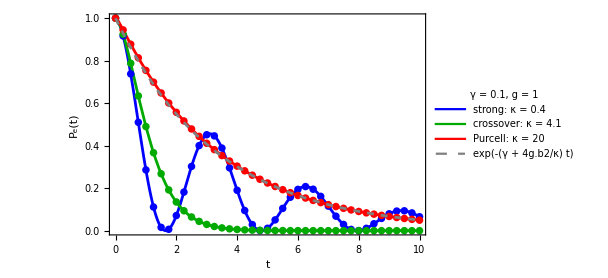

```mathematica
With[{regimeColours={Blue,Darker[Green],Red}},Show[Plot[Evaluate[(peExact[#1,#2][t]&)@@@regimes],{t,0,10},],ListPlot[atomProb[#,{0,10,0.25}]&/@evolutions,],]]
```

#### Vacuum Rabi splitting: transmission spectrum

What an experiment usually measures is not P_e(t) but a spectrum. Drive the cavity weakly with a laser of frequency ω_L and strength η, and record how many photons build up inside or the light leaks out through the mirror as a function of the detuning Δ = ν-ω_L. Going to the rotating frame subtracts ω_L(a^†a+σ_z/2) from H and also the drive term becomes η(a+a^†)

Set up the weak laser strength:

```mathematica
ηd=0.005;
```

Define the Hamiltonian:

```mathematica
Hdrive[Δ_]:=H-(ν-Δ) (SuperDagger[a]@a+1/2 QuantumOperator["Z",atomBasis])+ηd (a+SuperDagger[a]);
```

The steady state is the density matrix that the Lindblad generator ℒ sends to zero, 
ℒ ρ_ss=0. And we consider one more observation Δ enters H_drive linearly and the losses do not depend on it, so ℒ(Δ)=ℒ_0+Δ ℒ_1. Two super-operator instances per set of rates are enough, hence every detuning is then obtained with a linear-algebra solve

Steady state calculation:

```mathematica
liouvillianParts[κ_,γ_]:=With[{l0=QuantumOperator["Liouvillian"[Hdrive[0],{σminus,a},{γ,κ}]]["Matrix"]},{l0,QuantumOperator["Liouvillian"[Hdrive[1],{σminus,a},{γ,κ}]]["Matrix"]-l0}];
```

```mathematica
steadyState[{l0_,l1_},Δ_]:=With[{ρ=ArrayReshape[First[NullSpace[N[l0+Δ l1]]],{2 $FockSize,2 $FockSize}]},QuantumState[ρ/Tr[ρ],{2,$FockSize}]];
```

By input–output theory (a topic that is not covered), the outgoing field is proportional to the field inside, so the transmitted power is proportional to 
κ ⟨a^†a⟩. To normalize it  we divide by the same quantity for an empty cavity driven exactly on resonance. Without the atom, (ⅆ⟨a⟩)/ⅆt =-κ/2⟨a⟩-ⅈ η whose steady state is ⟨a⟩=-2ⅈ η/κ so ⟨(a^†a⟩)_empty=(4 η^2)/κ^2 → T =κ^2/(4 η^2)⟨a^†a⟩

Transmission obtained from the steady state:

```mathematica
transmissionQF[parts_,Δ_,κ_]:=(κ^2 QuantumMeasurementOperator[SuperDagger[a]@a][steadyState[parts,Δ]]["Mean"])/(4 ηd^2);
```

For weak driving the atom stays close to its ground state, ⟨a⟩ and ⟨σ_-⟩ obey two linear equations in steady state:

0=-(ⅈ Δ+κ/2)⟨a⟩-ⅈ g ⟨σ_-⟩,   0=-(ⅈ Δ + γ/2)⟨σ_-⟩-ⅈ g ⟨a⟩

Alternative method for weak driving:

```mathematica
cavityAmplitude=cav/.First[Solve[{0==-(ⅈ Δ+κ/2) cav-ⅈ gc atm-ⅈ ηd,0==-(ⅈ Δ+γ/2) atm-ⅈ gc cav},{cav,atm}]];
transmission[Δv_,κv_,γv_]=Simplify[(κ^2 Abs[cavityAmplitude]^2)/(4 ηd^2)/.{Δ->Δv,κ->κv,γ->γv}];
```

Plotting panel as function of κ assuming a fixed γ :

```mathematica
spectrumPanel[κv_,label_]:=With[{parts=liouvillianParts[κv,0.1]},Show[Plot[transmission[gc s,κv,0.1],{s,-3,3},],]];
```

Visualize the transmission spectra:

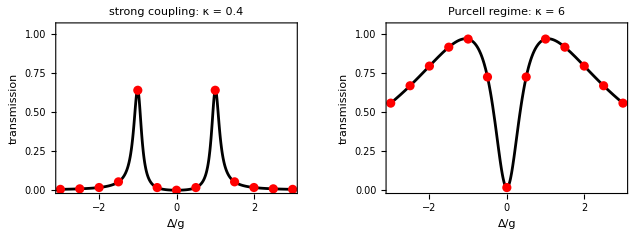

```mathematica
GraphicsRow[{spectrumPanel[0.4,"strong coupling: κ = 0.4"],spectrumPanel[6.,"Purcell regime: κ = 6"]}]
```

For strong coupling there are two peaks at Δ=±g.  This vacuum Rabi splitting is is the standard proof that an experiment has reached strong coupling. The peaks reach (κ/(κ+γ))^2 and not 1 because  the atom’s own decay steals light from the cavity mode

Verification of the maximum:

```mathematica
With[{κ=0.4,γ=0.1},{NMaximize[{transmission[gc s, κ, γ],-3<s<3},s],(κ/(κ+γ))^2}]
```

{{0.641584,{s→1.00495}},0.64}

For Purcell regime the cavity’s broad resonance has a deep narrow hole at 
Δ=0. The hole is the atom, it scatters the light out of the cavity mode, and its width is the Purcell-broadened atomic linewidth ≈ γ+4g^2/κ when κ>>γ

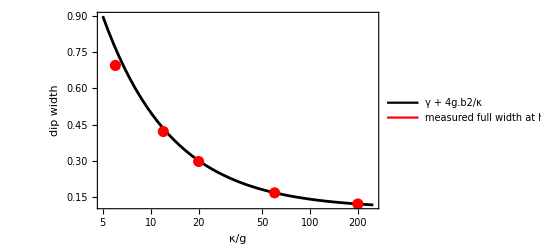

```mathematica
dipWidth[κv_]:=With[{t0=transmission[0,κv,0.1]},2 δ/. FindRoot[transmission[δ,κv,0.1]==(1+t0)/2,{δ,(0.1+4 gc^2/κv)/2}]];
Show[LogLinearPlot[0.1+4 gc^2/κv,{κv,5,250},PlotStyle->Black],ListLogLinearPlot[Table[{κv,dipWidth[κv]},{κv,{6,12,20,60,200}}],PlotStyle->Directive[Red,PointSize[0.02]]],Frame->True,Axes->False,FrameLabel->{"κ/g","dip width"},ImageSize->400,Epilog->Inset[LineLegend[{Black,Red},{"γ + 4g.b2/κ","measured full width at half depth"}],Scaled[{0.62,0.82}]]]
```

### 8.6 Phase space methods with Langevin/Fokker Planck equations

The master equation of section 8.3 evolves a density matrix. A cavity truncated at 
N photons needs N^2 numbers, and M modes need N^(2M). Phase-space methods trade the density matrix for a quasi-probability distribution W(α, t).  When that distribution obeys a Fokker–Planck equation,  we can sample it with classical stochastic trajectories that the cost grows linearly with the number of modes.

We will use the following workflow:

master equation -> Fokker-Planck equation ↔ Langevin/Ito (ⅆx=A(x)ⅆt+B(x)ⅆW)
where A and B are the drift and diffusion matrix of the process

For the s-parameter quasi-probability function, we can associate multiplying ρ by a and a^† to a differential operator affecting W(α,s). They are called Bopp differential operators and have the following rules:

a ρ -> (α + (1-s)/2 ∂_(α*))W ,     a^†ρ->(α*-(1-s)/2∂_α)W
ρ a-> (α - (1+s)/2 ∂_(α*))W  ,     ρ a^†→ (α*+(1-s)/2 ∂_α)W

Define the Bopp rules application:

```mathematica
Clear[α,αc]
```

```mathematica
α=(x+ⅈ p)/(√2);αc=(x-ⅈ p)/(√2);
dα[f_]:=(D[f, x]-ⅈ D[f, p])/(√2);
dαc[f_]:=(D[f, x]+ⅈ D[f, p])/(√2);
aρ[f_]:=α f+1/2 (1-s) dαc[f];
adρ[f_]:=αc f-1/2 (1+s) dα[f];
ρa[f_]:=α f-1/2 (1+s) dαc[f];
ρad[f_]:=αc f+1/2 (1-s) dα[f];
```

Basic definitions:

```mathematica
SetFockSpaceSize[8];
a:=AnnihilationOperator[]
```

Define a random density operator whose elements only fill up to $FockSize/2 , so all operator applications are determined exactly for the given cutoff:

```mathematica
ρ=QuantumState[RandomComplex[{-1-ⅈ,1+ⅈ},$FockSize/2],$FockSize]["Normalize"]["Operator"];
```

```mathematica
ρ["Matrix"]//MatrixPlot
```

-Graphics-

Calculate the s-ordered function:

```mathematica
quasi[op_]:=SOrderedFunction[op["MatrixQuantumState"],{x,p},s];
```

Verify the rules:

```mathematica
(Chop[Simplify[quasi[#1]-#2[quasi[ρ]]]]===0&)@@@{{a[ρ],aρ},{SuperDagger[a][ρ],adρ},{ρ[a],ρa},{ρ[SuperDagger[a]],ρad}}
```

{True,True,True,True}

#### From the master equation to a Fokker-Planck equation

Starting from the Lindblad master equation

ρ̇=-ⅈ[H, ρ]+∑_k γ_k(L_k ρ L_k^†-1/2 L_k^†L_k ρ-1/2 ρ L_k^†L_k)

If we consider the dissipators of photon loss and gain (L=a, L=a^†) and use the rules we derived their action on W is :

```mathematica
loss[f_]:=aρ[ρad[f]]-(adρ[aρ[f]]+ρa[ρad[f]])/2;
gain[f_]:=adρ[ρa[f]]-(aρ[adρ[f]]+ρad[ρa[f]])/2;
```

Every master equation we will explore in this section will be built from these pieces

Think of W as a cloud of points wandering through phase space. In a short time Δ t a point at x jumps by an amount Δ x, and we can define the following statistics:
The average jump per unit time A_i=⟨Δ x_i⟩/Δ t or drift , 
The spread of the jumps per unit time D_(i j)=⟨Δ x_i Δ x_j⟩/Δ t or diffusion
The skewness ⟨Δ x_i Δ x_j Δ x_k⟩/Δ t , and so on to even higher moments

Kramers and Moyal showed that the evolution of the density matrix can be written as a series in which the n-moment of the jumps multiply the n-th derivative of W:

∂_t W=-∂_i (A_i W)+1/2 ∂_i ∂_j (D_(i j)W)-1/6∂_i ∂_j ∂_k (…)+…

A drop of ink in a flowing river is the picture to keep in mind. The current carries the drop along (the first-derivative drift term), and molecular motion spreads it out (the second-derivative diffusion term). If the series stops after these two terms, it is the Fokker–Planck equation, and the cloud of points is an accurate representation a set of particles that drift and diffuse. However Pawula’s theorem states the series either stops at second order or goes on forever. Keeping a third or fourth term while dropping the rest generally produces “probabilities” that turn negative. For the Wigner function, linear damping and quadratic Hamiltonians stop exactly at second order, we will se later how to deal with Hamiltonians such as the Kerr effect.

Implementation of Kramers Moyal approach, a trick used is acting on  ⅇ^(u x + v p) turns every ∂_x into a u and every ∂_p  into v. So CoefficientRules in {u,v} lists the coefficients of each derivative

```mathematica
kramersMoyal[lindbladian_,s0_]:=Block[{s=s0},Module[{coefficients,moment},coefficients=CoefficientRules[Simplify[Exp[-u x-v p] lindbladian[Exp[u x+v p]]],{u,v}];moment[g_]:=Simplify[Total[((-1)^Total[#1] D[(#2 g), {x,#1⟦1⟧},{p,#1⟦2⟧}]&)@@@coefficients]];Association["Order"->Max[Total/@Keys[coefficients]],"Drift"->moment/@{x,p},"Diffusion"->Simplify[Outer[moment[#1 #2]-#1 moment[#2]-#2 moment[#1]&,{x,p},{x,p}]]]]]
```

For example, for a thermal bath with mean occupation n^— has loss at rate γ(n^—+1) and gain at rate γ n^—:

```mathematica
thermal[f_]:=γ (n̄+1) loss[f]+γ n̄ gain[f]
```

We keep s symbolic:

```mathematica
kramersMoyal[thermal,s]
```

<|Order→2,Drift→{-(x γ)/2,-(p γ)/2},Diffusion→{{1/2 (γ-s γ+2 γ n̄),0},{0,1/2 (γ-s γ+2 γ n̄)}}|>

All representations have the same drift amplitude relaxation with γ/2 behavior. But the noise depends on the specific representation ordering

#### Fokker-Planck to Langevin: the damped oscillator

The Fokker–Planck equation describes the whole cloud at once, how the density of points flows and spreads. Langevin motivated by studying Brownian motion, took the other view and followed a single particle. A classic example of a pollen grain in water obeys Newton’s law with two forces from the water a smooth friction that slows it down, and a rapidly fluctuating force from individual molecular impacts

m ẋ =-η v+ξ(t)

If we solve this equation many times with independent random forces, and construct a histogram from  the results, we can recover the density that the Fokker–Planck equation evolves

In the Itô form we use ⅆx=A ⅆt+B ⅆW during a short step Δ t we get a deterministic move A ⅆt along the drift and a random kick B ⅆ W where ⅆW is a gaussian increment with variance d t. The kick scales as √(d t) and not d t because independent kicks contribute variance adding, after N steps the displacement is √Ntimes a single kick, the familiar random-walk spreading. This is also why stochastic calculus differs from ordinary calculus

A single Langevin trajectory in phase space is not the path the quantum field “really” takes, it has no definite (x,p). It is a sampling device, each trajectory is one draw from the quasi-probability distribution, and only averages over many trajectories carry physical meaning

A second-order FPE with positive semidefinite D is equivalent to the Itô equation B=D^(1/2). ItoProcess takes this stochastic differential equation building it from the Kramers-Moyal coefficients

Langevin builder:

```mathematica
langevin[km_,init_]:=ItoProcess[Thread[{ⅆx[t],ⅆp[t]}==(km["Drift"] ⅆt+MatrixPower[km["Diffusion"],1/2].{ⅆw1[t],ⅆw2[t]}/.{x->x[t],p->p[t]})],{x[t],p[t]},{{x,p},init},t,{w1\[Distributed]WienerProcess[],w2\[Distributed]WienerProcess[]}]
```

Let’s compute the Wigner Fokker–Planck equation for the density ℙ(x,p,t) applied to the thermal bath, the expected result is

∂_t ℙ = ∂_x (γ/2 x ℙ)+∂_p (γ/2 p ℙ)+γ/2(n^—+1/2)(∂_x^2 +∂_p^2)ℙ

Get the Fokker-Planck equation from the “KolmogorovForwardEquation” property:

```mathematica
proc=langevin[kramersMoyal[thermal,0],{x0,p0}];
FullSimplify[proc["KolmogorovForwardEquation"]/.rulesFP]
```

p^(0,0,1)(x,p,t)==1/4 γ (2 n̄+1) ((∂^2 p(x,p,t))/(∂p ∂p)+(∂^2 p(x,p,t))/(∂x ∂x))+∂/(∂p)(1/2 p γ p(x,p,t))+∂/(∂x)(1/2 x γ p(x,p,t))

Which must coincide with the previous result at s=0:

```mathematica
Block[{s=0},Simplify[thermal[p[x,p,t]]==Activate[Last[proc["KolmogorovForwardEquation"]]]]]
```

True

Calculate symbolic moments from the process:

```mathematica
Simplify[{Mean[proc[t]],Covariance[proc[t]]},t>0&&γ>0]
```

{{ⅇ^(-(t γ)/2) x0,ⅇ^(-(t γ)/2) p0},{{1/2 ⅇ^(-t γ) (-1+ⅇ^(t γ)) (1+2 n̄),0},{0,1/2 ⅇ^(-t γ) (-1+ⅇ^(t γ)) (1+2 n̄)}}}

To get a quantum expectation value we also average over the initial Wigner function. For a coherent state |α_0⟩ that is a Gaussian centered at √2{Re(α_0),Im(α_0)} with covariance 1/2 𝟙 . The Wigner function gives symmetrically ordered moments so ⟨a^†a⟩=⟨|α|^2⟩_W-1/2

```mathematica
nOfT=FullSimplify[Expectation[1/2 (Total[Mean[proc[t]]^2]+Tr[Covariance[proc[t]]]),{x0,p0}\[Distributed]MultinormalDistribution[√2 {Re[α0],Im[α0]},IdentityMatrix[2]/2]]-1/2,t>0&&γ>0]
```

ⅇ^(-t γ) (Abs[α0]^2-n̄)+n̄

Alternatively, we can follow a Glauber P function approach ⟨a^†a⟩=⟨|α|^2⟩_(s->1) that is associated to normal ordering. For this process the initial coherent state is just a single point (a Dirac delta) and not a blob:

```mathematica
procP=langevin[kramersMoyal[thermal,1],√2 {Re[α0],Im[α0]}]
```

ItoProcess[{{-1/2 γ x[t],-1/2 γ p[t]},{{√(γ n̄),0},{0,√(γ n̄)}},{x[t],p[t]}},{{x,p},{√2 Re[α0],√2 Im[α0]}},{t,0}]

Expectation is not needed, recovering the same result:

```mathematica
FullSimplify[1/2 (Total[Mean[procP[t]]^2]+Tr[Covariance[procP[t]]])]
```

ⅇ^(-t γ) (Abs[α0]^2-n̄)+n̄

Clearly the steady-state behavior is that the field mean number of photons converges to n^—:

```mathematica
Assuming[n̄>=0 && γ>0,lim_(t->∞) %]
```

n̄

The same physics looks simpler in intensity and phase.  Defining ℐ=(x^2+p^2)/2=|α|^2 and φ=tan^-1(p/x) . Changing variables in Ito calculus is not the same as ordinary calculus and needs Itô’s lemma

We can use ItoProcessChangeVariables resource function for this:

```mathematica
polar=ResourceFunction["ItoProcessChangeVariables"][proc,{ℐ,φ},{ℐ==1/2 (x^2+p^2),φ==ArcTan[x,p]}];
```

It returns also an Ito process that we can access its properties:

```mathematica
{polar["Drift"],FullSimplify[polar["Diffusion"].polar["Diffusion"]ᵀ]}
```

{{γ/2+γ n̄-γ ℐ[t],0},{{γ (1+2 n̄) ℐ[t],0},{0,(γ+2 γ n̄)/(4 ℐ[t])}}}

The  constant γ (n^—+1/2) is the Ito term and it is the whole source of the thermal photons. The phase has no drift but diffuses at a rate proportional to 1/ℐ, the more intense the field the more slowly its phase disperses.

Let’s now do a numerical implementation with three methods: solving the PDE of the Fokker-Planck equation, sampling Langevin trajectories with RandomFunction and density matrix evolution with QuantumEvolve

Set up parameters, start from a coherent state with α_0=3 and a thermal bath with n^—=2:

```mathematica
nPaths=400;
tStep=0.02;
tEnd=4;
amplitude=3;
values={γ->1,n̄->2};
SetFockSpaceSize[50];
number=SuperDagger[a]@a;
```

The initial condition is the coherent state’s Wigner function from WignerRepresentation, an interpolating function on a grid:

```mathematica
ψ0=CoherentState[][amplitude];
w0=WignerRepresentation[ψ0,{-7,10},{-7,7},"GridSize"->200];
```

The PDE solution is a function wigner[x, p, t], with its arguments in the order of ℙ[x, p, t]:

```mathematica
wigner=NDSolveValue[{Activate[proc["KolmogorovForwardEquation"]]/.values,p[x,p,0]==w0[x,p],DirichletCondition[p[x,p,t]==0,True]},p,{t,0,tEnd},{x,p}∈Rectangle[{-7,-7},{10,7}],Method->{"PDEDiscretization"->{"MethodOfLines","SpatialDiscretization"->{"FiniteElement","MeshOptions"->{"MaxCellMeasure"->0.02}}}}];
```

Evolution with QuantumEvolve:

```mathematica
ρt=QuantumEvolve[0 number,(√{γ (n̄+1),γ n̄}/.values) {a,SuperDagger[a]},ψ0,{t,0,tEnd}];
```

Sampling mean photon number:

```mathematica
nQF=Table[{τ,QuantumMeasurementOperator[number][ρt[τ]]["Mean"]},{τ,0,tEnd,tEnd/10}];
```

We show the time-lapse of the cloud. The trajectories are frozen at four instants, one color per instant, and each dot is one trajectory at that moment. The circle of the same color is the PDE solution at that instant, drawn one standard deviation from its center. Three individual trajectories are drawn in light gray. Each one is a jagged path, the drift carries it towards the origin, and the noise kicks it sideways at every step

And we also observe the two effects, the center of the cloud ⟨x⟩ is moved by the drift it decays to the origin as ⅇ^(-γ t/2).  The spread of the cloud is set by the competition of drift and diffusion.  The drift squeezes the initial spread 1/2  by ⅇ^(–γ t) while the noise feeds new spread until the variance settles at the thermal value n^—+1/2=2.5

Visualize the result, we show up to 100 trajectories in the plot but all enter the average calculation. The shaded bands show how far the dots should scatter two standard deviations of the Monte Carlo error

timeLapse and driftDiffusion code

```mathematica
times={0,0.5,1.5,4};
colors={Black,Blue,Darker[Green],Red};
cloudAt[τ_]:=paths[[All,Round[τ/tStep]+1]];
centre[τ_]:=First[Mean[proc[τ]]]/. values/. x0->Sqrt[2] amplitude;

nShow=Min[100,nPaths];
timeLapse=Show[ListLinePlot[paths[[;;3]],],MapThread[ListPlot[cloudAt[#1][[;;nShow]],]&,{times,colors}],MapThread[ContourPlot[wigner[x,p,#1],{x,-6,9},{p,-6,6},]&,{times,colors}],];

meanCurve=First[Mean[proc[t]]]/. values/. x0->Sqrt[2] amplitude;
varianceCurve=Covariance[proc[t]][[1,1]]+Exp[-γ t]/2/. values;
stats=Table[{τ,Mean[cloudAt[τ][[All,1]]],Variance[cloudAt[τ][[All,1]]]},{τ,0,tEnd,10 tStep}];
driftDiffusion=Show[Plot[Evaluate[{meanCurve+2 Sqrt[varianceCurve/nPaths],meanCurve-2 Sqrt[varianceCurve/nPaths],varianceCurve (1+2 Sqrt[2/(nPaths-1)]),varianceCurve (1-2 Sqrt[2/(nPaths-1)])}],{t,0,tEnd},],Plot[Evaluate[{meanCurve,varianceCurve}],{t,0,tEnd},],];
```

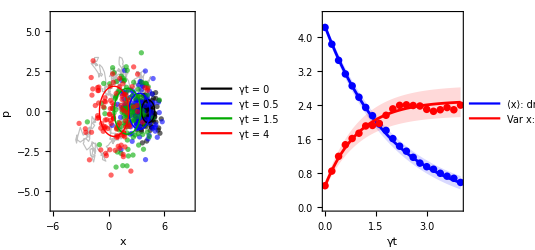

```mathematica
GraphicsRow[{timeLapse,driftDiffusion}]
```

Compare the mean photon number using the three methods:

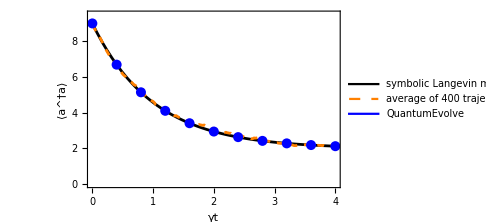

```mathematica
Show[Plot[nOfT/. values/. α0->amplitude,{t,0,tEnd},PlotStyle->Black],ListLinePlot[Transpose[{Range[0,tEnd,tStep],nLangevin}],],]
```

#### Worked Example: squeezing in a parametric oscillator

A degenerate parametric oscillator driven by a strong classical pump is described, in the pump’s rotating frame, by

H = ⅈ ε/2((a^†)^2-a^2),     L=√κ a

With the pump held fixed (no depletion) the problem is quadratic, the FPE is exactly second order, and nothing is approximated. The commutator reads as -ⅈ[H, ρ]=ε/2((a^†)^2 ρ-ρ (a^†)^2-a^2 ρ+ρ a^2) and we can use the previously defined photon loss action

```mathematica
parametric[f_]:=ε/2 (adρ[adρ[f]]-ρad[ρad[f]]-aρ[aρ[f]]+ρa[ρa[f]])+κ loss[f]
```

Look at the noise in the three most important representations:

```mathematica
kramersMoyal[parametric,#]["Diffusion"]&/@{1,0,-1}
```

{{{ε,0},{0,-ε}},{{κ/2,0},{0,κ/2}},{{-ε+κ,0},{0,ε+κ}}}

The P representation has negative diffusion in the p quadrature, which means no 
well behaved P function and no Langevin equation in this representation. This is the phase space signature of nonclassical light

The Wigner equation is perfectly well behaved:

```mathematica
km=kramersMoyal[parametric,0];
opo=langevin[km,{0,0}];
```

We get the expected ∂_t ℙ=-∂_x ((ε-κ/2)x ℙ)+∂_p ((ε+κ/2)p ℙ)+ κ/4(∂_x^2 +∂_p^2)ℙ

```mathematica
FullSimplify[opo["KolmogorovForwardEquation"]/.rulesFP]
```

p^(0,0,1)(x,p,t)==1/4 κ ((∂^2 p(x,p,t))/(∂p ∂p)+(∂^2 p(x,p,t))/(∂x ∂x))+∂/(∂x)(1/2 x (κ-2 ε) p(x,p,t))+∂/(∂p)(1/2 p (2 ε+κ) p(x,p,t))

The pump amplifies x and de-amplifies p, against the same vacuum noise. The drift is linear A=J x

```mathematica
km["Drift"]
```

{x (ε-κ/2),-1/2 p (2 ε+κ)}

The stationary covariance σ solves the Lyapunov equation J σ +σ Jᵀ+D=0:

```mathematica
σs=Simplify[LyapunovSolve[D[km["Drift"], {{x,p}}],-km["Diffusion"]],{κ,ε}∈Reals]
```

{{κ/(-4 ε+2 κ),0},{0,κ/(4 ε+2 κ)}}

The x quadrature diverges at the threshold κ=ε/2 while p is squeezed below vacuum value

```mathematica
N[lim_(ε->κ/2) 10 Log10[2 σ⟦2,2⟧]]
```

-3.0103

The intracavity field can be squeezed by at most a factor of two or 3 dB limit

For the comparison, the master equation is solved with QuantumEvolve:

```mathematica
SetFockSpaceSize[40];
steadyState[εv_]:=QuantumEvolve[1/2 ⅈ εv (SuperDagger[a]@SuperDagger[a]-a@a),{a},FockState[0],{t,0,80}][80]["Normalize"];
```

We use CovarianceMatrix for the quadrature covariance elements:

```mathematica
noisedB[εv_]:=10 Log10[2 Diagonal[CovarianceMatrix[steadyState[εv]]]];
qf=Table[With[{dB=noisedB[εv]},{{εv,dB⟦2⟧},{εv,dB⟦1⟧}}],{εv,0,0.4,0.1}];
```

Define the trajectory cloud and the Wigner representation of the steady state:

```mathematica
cloud=First[RandomFunction[opo/. {κ->1,ε->0.3},{0,4000,0.05}]["ValueList"]][[400;; ;;10]];
wSteady=WignerRepresentation[steadyState[0.3],{-4,4},{-4,4}];
```

Time is in units of 1/κ, we show one long Langevin trajectory sampled after it reaches steady state with the steady-state Wigner contour from  (red) and the vacuum contour (dashed), both at. And also the noise in each quadrature against pump strength, the Lyapunov formula (lines) against the master equation (dots).

```mathematica
phase=Show[ListPlot[cloud,],ContourPlot[wSteady[x,p],{x,-4,4},{p,-4,4},],ContourPlot[Exp[-x^2-p^2]/π,{x,-4,4},{p,-4,4},],];
```

```mathematica
noise=Show[Plot[Evaluate[{10 Log10[2 σ⟦2,2⟧],10 Log10[2 σ⟦1,1⟧]}/. κ->1],{ε,0,0.49},],ListPlot[Transpose[qf],],Plot[-10 Log10[2],{ε,0,0.5},],];
```

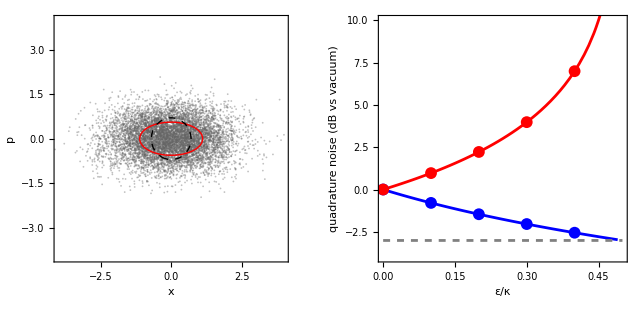

```mathematica
GraphicsRow[{phase,noise}]
```

#### Kerr effect: truncated Wigner approximation

So far every FPE stopped at second order, so the Langevin description was exact. However, take the Kerr oscillator H=χ (a^†)^2 a^2 whose commutator  is -ⅈ χ((a^†)^2 a^2 ρ-ρ (a^†)^2 a^2)

Translating the equation to our formalism:

```mathematica
kerr[f_]:=-ⅈ χ (adρ[adρ[aρ[aρ[f]]]]-ρa[ρa[ρad[ρad[f]]]]);
```

Obtain the “Order” and check if the diffusion matrices are positive semidefinite for the Q, W and P representations:

```mathematica
kramersMoyal[kerr,#]["Order"]&/@{-1,0,1}
```

{2,3,2}

```mathematica
PositiveSemidefiniteMatrixQ[kramersMoyal[kerr,#]["Diffusion"]]&/@{-1,0,1}
```

{False,True,False}

The Q and P equations are second order, but their diffusion matrices are not positive semidefinite. The Wigner equation has positive (in fact zero) diffusion, but it is third order. A Langevin equation can only carry the first two orders, so the difference between the full Wigner equation and the forward equation of its ItoProcess is what gets lost

Compute that difference:

```mathematica
kerrKM=kramersMoyal[kerr,0];
kerrProc=langevin[kerrKM,{x0,p0}];
Block[{s=0},Simplify[kerr[p[x,p,t]]-Activate[Last[kerrProc["KolmogorovForwardEquation"]]]]]
```

1/4 χ (-x p^(0,3,0)[x,p,t]+p p^(1,2,0)[x,p,t]-x p^(2,1,0)[x,p,t]+p p^(3,0,0)[x,p,t])

Which can be reduced to χ/4(p ∂_x -x ∂_p)∇^2 (…) :

```mathematica
Factor[%/.Derivative[i_,j_,0][p][x,p,t]:>Subscript["∂", x]^i Subscript["∂", p]^j]
```

-1/4 χ (x ∂_p-p ∂_x) (∂_p^2 +∂_x^2)

The truncated Wigner approximation (TWA) discards this term. The drift is -2 ⅈ χ(|α|^2-1)α  that grows like |α|^3 while the third order coefficient grows like |α|. For large amplitudes the truncation is a semiclassical expansion in 1/|α|^2

Express the drift in intensity form:

```mathematica
Factor[With[{dr=(kerrKM["Drift"].{1,ⅈ})/(√2)},dr/.{p^2+x^2->Abs[α]^2,x->√2 α-ⅈ p}]]
```

-ⅈ α χ (Abs[α]^2-2)

Each phase-space point rotates about the origin at a speed set by its own intensity
Something the TWA gets right is the squeezing. Start from a coherent state |α_0⟩ with n_0=|α_0|^2 photons, its Wigner function is a blob with the vacuum noise. Points on the outer edge of the disk have more intensity, so they rotate faster than points on the inner edge, and the disk is sheared into a tilted ellipse. A sheared disk is a squeezed state, some quadrature has less noise than the vacuum. In the TWA, though, it comes from nothing more than the initial vacuum noise carried along by the classical drift, which is not  lost by the truncation

The TWA implementation can be done in three main steps: drawing samples from the initial Wigner function, evolving every sample independently with the truncated Langevin equation and computing averages say for example ⟨a⟩≈ α^— or ⟨a^†a⟩≈OverBar[Abs[α]^2]-1/2

Set TWA parameters:

```mathematica
nTWA=4000;
nSteps=400;
chiRule = χ->1;
```

With n_TWA= 4000 samples, a separate RandomFunction call per sample is slow. Because the noise is additive (a constant B), all samples can be advanced together as one 2×n_TWA packed array, with the stochastic Heun step

TWA helper functions:

```mathematica
drift[{x_,p_}]=kerrKM["Drift"]/.chiRule;
B=MatrixPower[kerrKM["Diffusion"]/. chiRule,1/2];
heun[δt_][y_,δw_]:=With[{yp=y+δt drift[y]+B.δw},y+δt (drift[y]+drift[yp])/2+B.δw];
```

twaRun returns a list of nSteps + 1 clouds, one per time step, each a 2× n_TWA array holding the x and p of every trajectory

```mathematica
twaRun[n0_,tmax_]:=With[{δt=tmax/nSteps},FoldList[heun[δt],Transpose@RandomVariate[MultinormalDistribution[{√(2 n0),0},IdentityMatrix[2]/2],nTWA],RandomVariate[NormalDistribution[0,√δt],{nSteps,2,nTWA}]]]
```

Kerr “exact” evolution from QuantumEvolve using an appropriate truncation size that is big enough to get really accurate results:

```mathematica
kerrExact[n0_,tmax_]:=Block[{$FockSize=Ceiling[n0+8 √n0+15]},QuantumEvolve[SuperDagger[a]@SuperDagger[a]@a@a,CoherentState[][√N[n0]],{t,0,tmax}]]
```

The quadrature covariance is needed at about 150 instants, so we take the quadrature matrices once per dimension and form the moments with the state vector:

```mathematica
quadratures[dk_]:=quadratures[dk]=(#1["Matrix"]&)/@(√2 QuadratureOperators[dk]);
```

```mathematica
quadratureMoments[ψ_QuantumState]:=With[{v=ψ["Normalize"]["StateVector"],R=quadratures[ψ["Dimension"]]},With[{A=R.v},With[{m=Re[A*.v]},{m,Re[A*.Aᵀ]-Outer[Times,m,m]}]]];
```

Squeezing limit in dB  comparison:

```mathematica
squeezing[c_]:=10 Log10[2 Min[Eigenvalues[c]]]
```

Define run parameters, we use photon number n_0=4,25,100 each up to the same scaled time τ_max=χ t n_0^(2/3):

```mathematica
n0s={4,25,100};
τmax=1.;
nExact=100;
```

Compute the squeezing curves:

```mathematica
runs=AssociationMap[{twaRun[#1,τmax #1^(-2/3)],kerrExact[#1,τmax #1^(-2/3)]}&,n0s];
```

```mathematica
squeezingCurves[n0_,{clouds_,exact_}]:=With[{tmax=τmax n0^(-2/3)},{Transpose[{Subdivide[0,τmax,nSteps],(squeezing[Covariance[Transpose[#1]]]&)/@clouds}],Table[{τ n0^(2/3),squeezing[Last[quadratureMoments[exact[τ]]]]},{τ,0,tmax,tmax/nExact}]}];
curves=KeyValueMap[squeezingCurves,runs];
```

Visualize the curves:

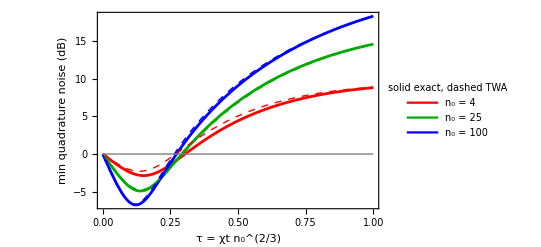

```mathematica
With[{colors = {Red,Darker[Green],Blue}},Show[ListLinePlot[curves[[All,2]],],ListLinePlot[curves[[All,1]],],Plot[0,{τ,0,τmax},],]]
```

The TWA gets the expected behavior. It reproduces the dip, its depth to within a few tenths of a dB, its position in τ  and the later rise. The optimal squeezing time shrinks like n_0^(-2/3)  the one-axis-twisting scaling due to the similarities in structure of the Kerr non linear Hamiltonian and the spin S_z^2.

Function for preparing Wigner plot panels:

```mathematica
kerrPanels[n0_,τ_,{x1_,x2_},{p1_,p2_}]:=Module[{clouds,exact,k=Round[τ nSteps/τmax],cloud,rot,w,wmax,colour},{clouds,exact}=runs[n0];
cloud=clouds[[k+1]];
rot=RotationMatrix[Arg[Mean[cloud⟦1⟧+ⅈ cloud⟦2⟧]]];
w=WignerRepresentation[exact[k τmax/nSteps n0^(-2/3)],{-13,13},{-13,13},"GridSize"->300];
wmax=Max[Abs[Table[w@@(rot.{x,p}),{x,x1,x2,(x2-x1)/100},{p,p1,p2,(p2-p1)/100}]]];
colour=Blend[{Blue,White,Red},(1+#/wmax)/2]&;
{DensityPlot[w@@(rot.{x,p}),{x,x1,x2},{p,p1,p2},],SmoothDensityHistogram[Transpose[Transpose[rot].cloud],0.15,]}];
```

Visualize the phase space evolution at three instants:

```mathematica
Grid[{kerrPanels[25,0,{4,10},{-3,3}],kerrPanels[25,0.15,{4,10},{-3,3}],kerrPanels[25,0.7,{-9,9},{-9,9}]}]
```

-Graphics-

Compare the inside of the two crescents. The exact Wigner function has interference fringes there alternating red and blue. A Wigner function is allowed to go negative, and the exact one does. The fringes are produced by the third-order term found above, the one the TWA drops. Without it, the TWA evolution is a classical flow of points (plus diffusion when there is damping). A flow only carries weight around phase space, it never changes its sign. Starting from the positive coherent-state Wigner function, the TWA therefore stays positive for all times and cannot build the fringes, which is why its panel is red only.

The TWA  can start from a negative Wigner function by giving the samples signed weights, this means carrying that negativity along. Creating new interference still needs the third order term

Initialization

Load the Quantum Framework:

```mathematica
Needs["Wolfram`QuantumFramework`"]
```

Load the second quantization tools:

```mathematica
Needs["Wolfram`QuantumFramework`SecondQuantization`"]
```

Useful definitions:

```mathematica
a := AnnihilationOperator[]
```

Helper rules  for simplification of inactive differential equations:

```mathematica
rulesFP={Inactive0__:>0,-Inactivearg_var_Symbol:>InactiveSimplify[-arg]var,Inactive(c_ (P:p[__]))v1_Symbolv2_Symbol/;FreeQ[c,v1]&&FreeQ[c,v2]:>c InactivePv1v2};
```

Exercises

Load the Quantum Framework paclet:

Needs["Wolfram`QuantumFramework`"]
Needs["Wolfram`QuantumFramework`SecondQuantization`"]

What jump operator do you think represents dephasing for a bosonic mode? Generate an animation of the evolution of the density matrix of a uniform superposition state, under the dephasing channel (with  H=0)

Solution

Generate a uniform superposition state:

ρ = QuantumState["UniformSuperposition",$FockSize];

Dephasing can be modelled with the jump operator a^†a:

ℒ = QuantumOperator["Liouvillian"[ None,{a["Dagger"]@a},{κϕ}],"Parameters"->{κϕ}];

Evolution of the state:

evolved =QuantumEvolve[ⅈ ℒ[0.2], ρ,{t,0,10}];

Get frames:

frames = Table[MatrixPlot[evolved[t]["DensityMatrix"],ColorFunction->"RedBlueTones",PlotLegends->All, PlotLabel->StringForm["t = ``",Round[t,0.01]],ImageSize->300,ImageMargins->20,LabelStyle->13],{t,10^-6,5,0.1}];

Export the GIF:

Export[NotebookDirectory[]<>"Dephasing.GIF",frames,"GIF","DisplayDurations"->Reverse@Subdivide[0.1,0.5,Length[frames]-1]];

Energy exchange between cavities (allowing decay) can be modelled with the jump operator (μ a_1 - λ a_2^†), where μ and λ are parameters. Consider an initial state |1,1⟩ and μ>λ. How does the entanglement of the two mode system behaves as function of time?

Solution

Set the size of the Fock space:

SetFockSpaceSize[10];

Operators of the two modes:

{a,b}=Array[AnnihilationOperator[{#}]&,2];

Initial state:

ρ0 = FockState[{1,1}];

Setting μ and λ:

{μ,λ}={0.6,0.2};

Build Liouvillian with jump operator μ a - λ b^†:

ℒ =QuantumOperator["Liouvillian"[None,{μ a - λ b^†},{0.6}]];

Evolve the state:

evolved=QuantumEvolve[I ℒ,ρ0,{t,0,4}];

Plot the measure of entanglement:

ListLinePlot[Table[QuantumEntanglementMonotone[evolved[t],{{1},{2}},"LogNegativity"],{t,0,4,0.1}],DataRange->{0,4},AxesLabel->{"t","LogNegativity"},PlotRange->All]

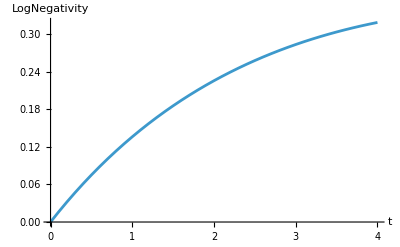

We saw the dissipative Jaynes-Cummings with a Fock state, now observe how collapse and revivals change with dissipation. The point of this exercise is to encourage exploration and determine relevant parameters. There are different regimes of interaction, so changing the Hamiltonian parameters and the γ rates can result in diverse dynamics.

Solution

Set the truncation size and relevant parameters:

SetFockSpaceSize[20];
ν = 8.;   
ω = 8.;   
gc = 10.; 
γ1 = 0.5;
γ2 = 0.5;
a:= AnnihilationOperator[{2}];

Hamiltonian:

H =  ν a^†@a+ 1/2 ω QuantumOperator["Z",atomBasis]+gc (σplus@a+σminus@a^†);

Master equation set up:

decayAtom = σminus@QuantumOperator["I"[$FockSize],{2}];
lossField = QuantumOperator["I",atomBasis]@a;

ℋ = QuantumOperator["Hamiltonian"[H, {decayAtom, lossField}, {γ1, γ2}]];

Initial state:

ρ0 =QuantumTensorProduct[QuantumState["1",atomBasis],CoherentState[][3.]];

Evolution:

evolved = QuantumEvolve[ℋ, ρ0,{t,0,10}];

Plotting results:

probs = atomProb[evolved,{0,10,0.1}];
ListLinePlot[probs,InterpolationOrder->2,PlotRange->All,PlotStyle->Red]

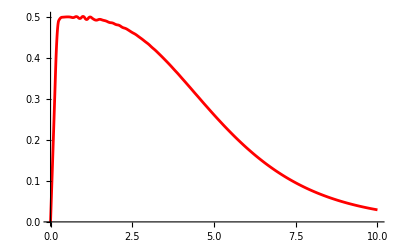

Comparing with the case without dissipation, already with γ_1=γ_2=0.5 all oscillations disappear:

Show[%326,%356]

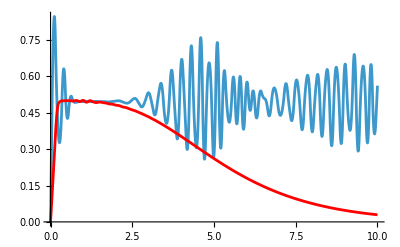

For the thermal bath keep s symbolic and read off how the diffusion depends on n̄ and s. Build the Langevin process from it, start from the s-ordered function of |α₀⟩ (a Gaussian with covariance (1−s)/2·𝟙 for s<1), and repeat the expectation calculation with the appropriate ordering correction. Show that the result agrees for every s. What is the long-time variance of the cloud, and why is it n̄ only after the correction? Finally, set s = 1 and n̄ = 0  and compute the covariance of the process and explain why the P-representation Langevin equation needs no random numbers at all.

Solution

Thermal bath:

thermal[f_]:=γ (n̄+1) loss[f]+γ n̄ gain[f]

Obtain the diffusion from Kramers-Moyal:

kmS=kramersMoyal[thermal,s];
kmS["Diffusion"]

{{1/2 (γ-s γ+2 γ n̄),0},{0,1/2 (γ-s γ+2 γ n̄)}}

Langevin equation process:

procS=langevin[kmS,{x0,p0}];

Expectation calculation:

Expectation[1/2 (Total[Mean[procS[t]]^2]+Tr[Covariance[procS[t]]]),{x0,p0}\[Distributed]MultinormalDistribution[√2 {Re[α0],Im[α0]},1/2 (1-s) IdentityMatrix[2]]]

-1/2 ⅇ^(-t γ) (-ⅇ^(t γ)+ⅇ^(t γ) s-2 Im[α0]^2+2 n̄-2 ⅇ^(t γ) n̄-2 Re[α0]^2)

The correction is (1-s)/2 and we get the same result that was obtained:

FullSimplify[%-(1-s)/2-(ⅇ^(-t γ) (Abs[α0]^2-n̄)+n̄)]

0

The steady-state cloud is the s-ordered function of a thermal state, its width is the thermal photons plus the ordering’s vacuum share. Only after subtracting (1−s)/2 we get  ⟨a^†a⟩=n^—

Limit[1/2 Tr[Covariance[procS[t]]],t→∞,Assumptions→γ>0]

n̄-s/2+1/2

Compute the P representation covariance:

procP=langevin[kmS/.{s→1,n̄→0},√2 {Re[α0],Im[α0]}];
{Covariance[procP[t]],FullSimplify[1/2 Total[Mean[procP[t]]^2]]}

{{{0,0},{0,0}},ⅇ^(-t γ) α0 Conjugate[α0]}

The ordering share (1-s)/2 is zero, normal ordering carries no vacuum noise. Also at n^—=0 there is thermal noise, and the P function of |α_0⟩ is single point so no random starting point . That is why no random number involved and the exact trajectory is |α_0⟩ -> |α_0 ⅇ^(-γ t/2)⟩

References

Gerry, Christopher C., and Peter L. Knight. Introductory Quantum Optics. Cambridge: Cambridge University Press, 2005.

Breuer, Heinz-Peter, and Francesco Petruccione. The Theory of Open Quantum Systems. Oxford: Oxford University Press, 2002.

Banerjee, Subhashish. Open Quantum Systems: Dynamics of Nonclassical Evolution. Singapore: Springer, 2018

Barnett, Stephen M., and Paul M. Radmore. Methods in Theoretical Quantum Optics. Oxford: Oxford University Press, 1997.

Carmichael, Howard J. Statistical Methods in Quantum Optics 1: Master Equations and Fokker-Planck Equations. Berlin: Springer, 1999

Scully, Marlan O., and M. Suhail Zubairy. Quantum Optics. Cambridge: Cambridge University Press, 1997.

Walls, D. F., and Gerard J. Milburn. Quantum Optics. 2nd ed. Berlin: Springer, 2008.